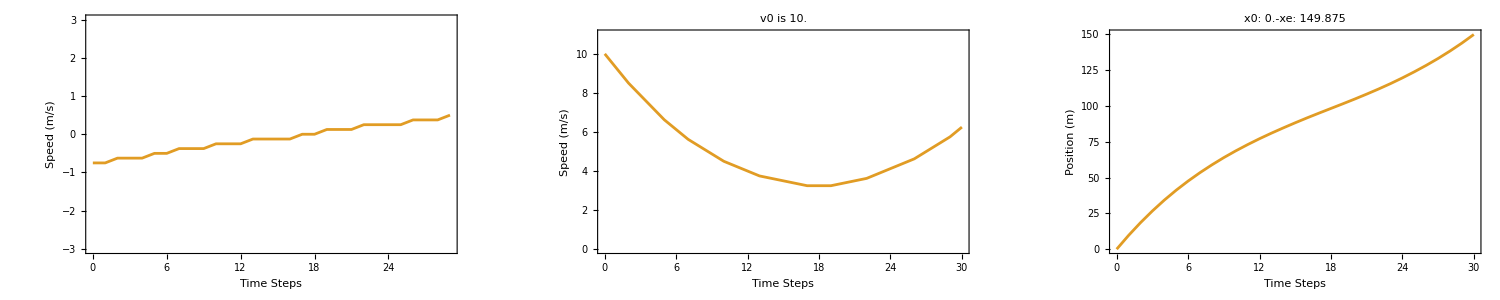

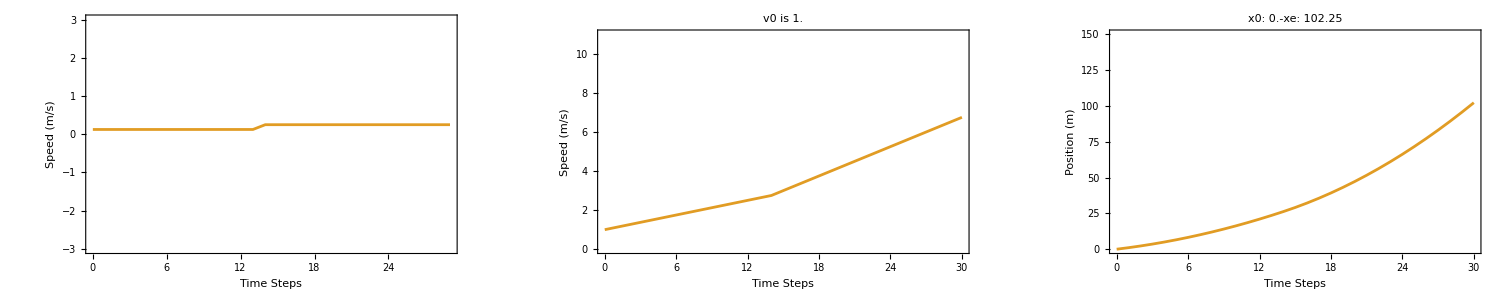

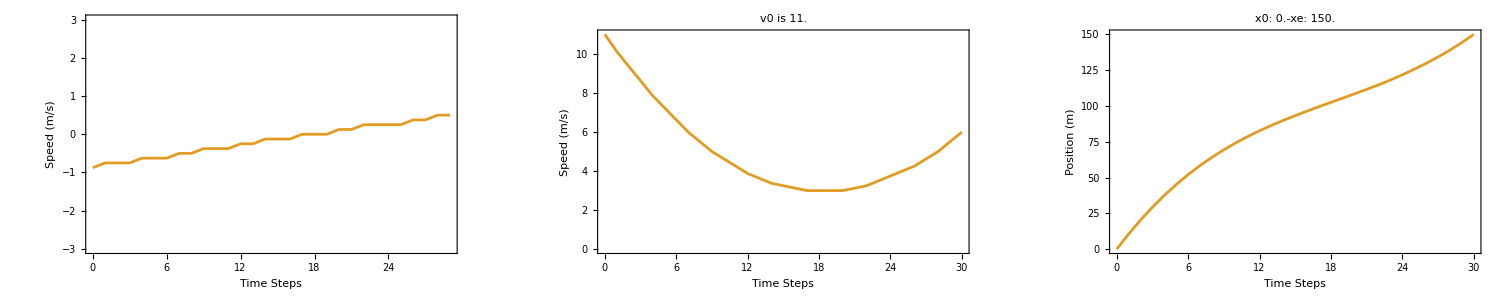

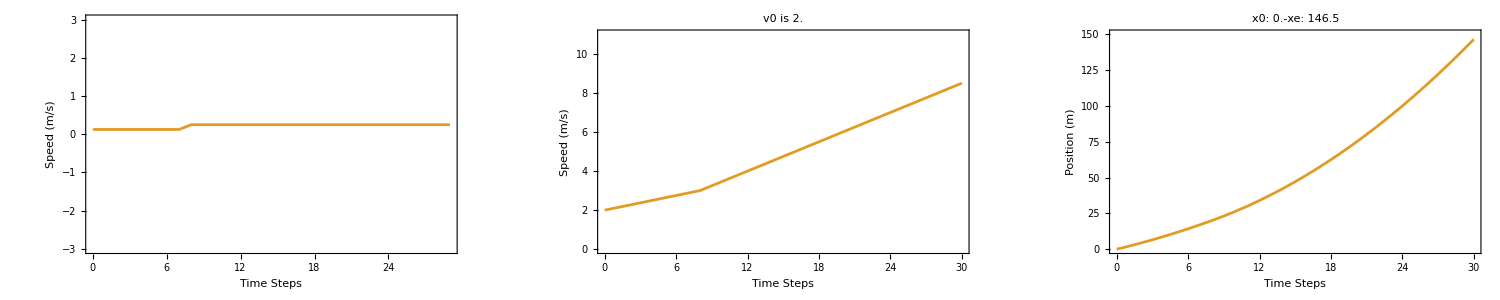

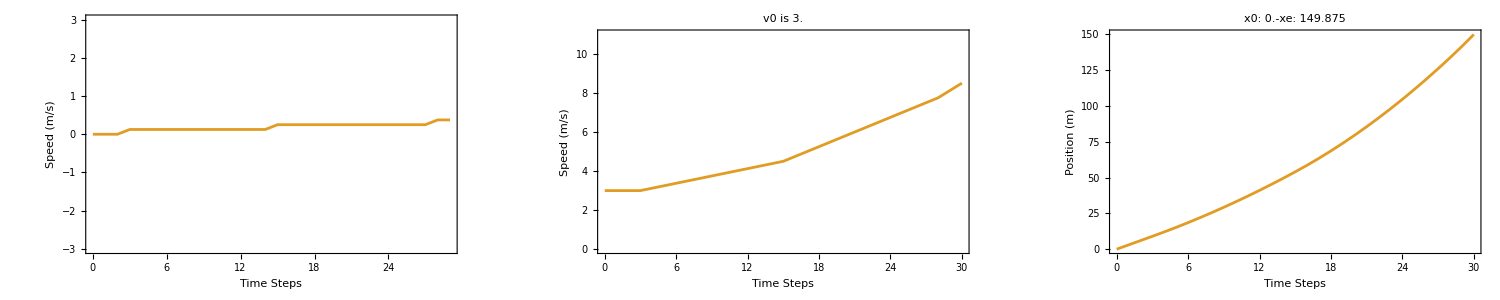

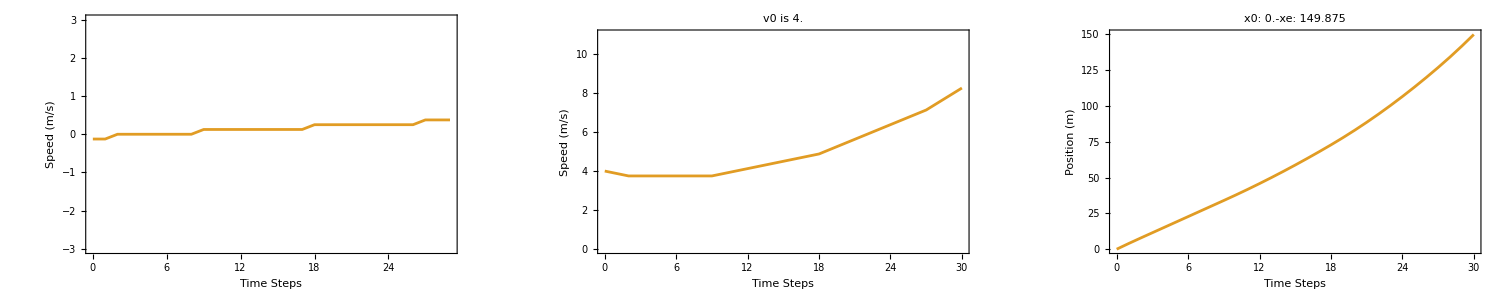

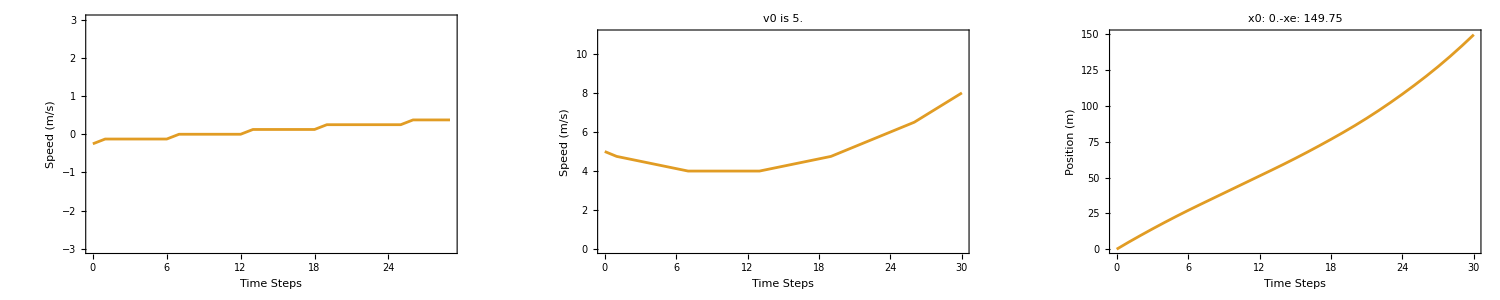

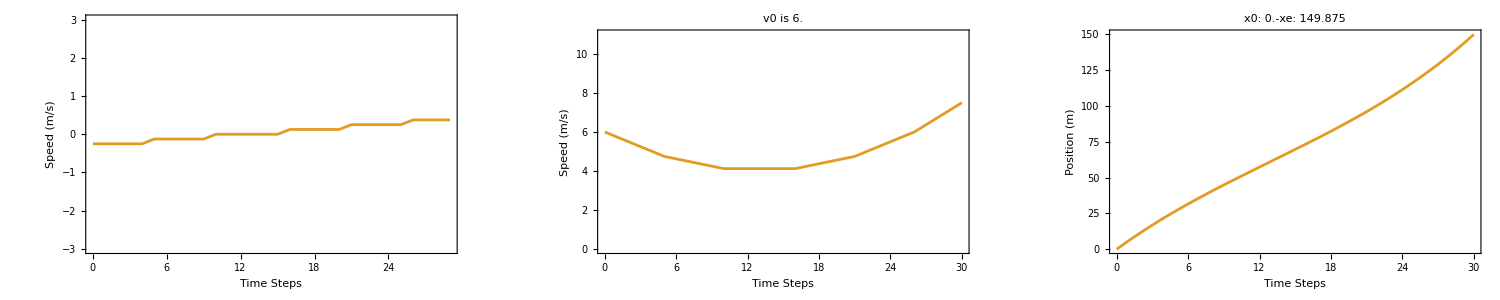

```mathematica
ClearAll["Global'*"]

dataFolder=StringJoin[NotebookDirectory[],"results_sdp/deterministic/"];
SetDirectory[dataFolder];
files=FileNames[];

pos={};speed={};accel={};vmin={};vmax={};xmin={};xmax={};initx={};initv={};inita={};dddpa={};dddpv={};dddpx={};
For[i=1,i≤Length[files]-1,i++,
data=Import[files[[i]],"Table"];
steps=data[[1;;,1]];
controlSteps=Delete[data[[1;;,1]],Length[steps]];
AppendTo[pos,data[[1;;,2]]];
AppendTo[speed,data[[1;;,3]]];
AppendTo[accel,Drop[data[[1;;,4]],-1]];
AppendTo[initv,data[[1;;,6]]];
AppendTo[initx,data[[1;;,5]]];
AppendTo[inita,Drop[data[[1;;,7]],-1]];
AppendTo[dddpv,data[[1;;,9]]];
AppendTo[dddpx,data[[1;;,8]]];
AppendTo[dddpa,Drop[data[[1;;,10]],-1]];
]

controlSteps;
For[i=1,i≤Length[files]-1,i++,
(*For[i=1,i≤3,i++,*)
p1=ListLinePlot[{Transpose[{controlSteps,accel[[i]]}]},
PlotRange->{Automatic,{-3,3}},LabelStyle->{FontFamily->"Constantia", FontSize->28,Bold},PlotStyle->{{Thickness[0.005],ColorData[97,"ColorList"][[2]]}},
TicksStyle->Directive[FontSize->24],AxesStyle->Thickness[0.001],Frame->{True,True,False,False},FrameLabel->{"Time Steps","Speed (m/s)",None,None}(*,ImageSize->500*)];
p2=ListLinePlot[{Transpose[{steps,speed[[i]]}]},
PlotRange->{Automatic,{0,11}},LabelStyle->{FontFamily->"Constantia", FontSize->28,Bold},PlotStyle->{{Thickness[0.005],ColorData[97,"ColorList"][[2]]}},
TicksStyle->Directive[FontSize->24],AxesStyle->Thickness[0.001],Frame->{True,True,False,False},FrameLabel->{"Time Steps","Speed (m/s)",None,None},
PlotLabel->StringForm["v0 is ``",speed[[i,1]]](*,ImageSize->500*)];
p3=ListLinePlot[{Transpose[{steps,pos[[i]]}]},
PlotRange->{Automatic,{0,150}},LabelStyle->{FontFamily->"Constantia", FontSize->28,Bold},PlotStyle->{{Thickness[0.005],ColorData[97,"ColorList"][[2]]}},
TicksStyle->Directive[FontSize->24],AxesStyle->Thickness[0.001],Frame->{True,True,False,False},FrameLabel->{"Time Steps","Position (m)",None,None},
PlotLabel->StringForm["x0: ``-xe: ``",pos[[i,1]],pos[[i,-1]]](*,ImageSize->500*)];
GraphicsGrid[{{p1,p2,p3}},ImageSize->1500]//Print
]

(*defBlue=ColorData[97,1];
defOrange=ColorData[97,2];
defGreen=ColorData[97,3];
fontSize=58;
n = Length[files]-1;

SetDirectory[NotebookDirectory[]];*)
(*For[i=1,i≤n,i++,
llp=ListLinePlot[{Transpose[{controlSteps,accel[[i]]}],Transpose[{controlSteps,inita[[i]]}]},
Filling->None,
Joined->True,
(*GridLines->{{0,10,20,30},{-0.5,-0.25,0,0.25,0.5}},*)
GridLines->{{0,10,20,30},{-1, -0.75, -0.5,-0.25,0,0.25,0.5}},
PlotRange->{{0,30},{-1,0.55}},
PlotRange->{{0,30},Automatic},
LabelStyle->{FontFamily->"Constantia", FontSize->fontSize-6,Bold},
PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue}},
AxesStyle->Thickness[0.001],
ImageSize->1000,
PlotStyle->PointSize[Large],
Frame->{True,True,False,False},
FrameTicks->{{{-1.0,-0.75,-0.5,-0.25,0,0.25,0.5},None},{{0,10,20,30},None}},
FrameLabel->{"Time Steps","Acceleration (m/s^2)",None,None}
];
llp2=ListLinePlot[{Transpose[{steps,speed[[i]]}],Transpose[{steps,initv[[i]]}]},
Filling->None,
Joined->True,
GridLines->Automatic,
PlotRange->{Automatic,{0,10.5}},
LabelStyle->{FontFamily->"Constantia", FontSize->fontSize,Bold},
PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue},{Thickness[0.007],Dashing[0.01],Red},{Thickness[0.007],Dashing[0.01],Red}},
AxesStyle->Thickness[0.001],
ImageSize->1000,
PlotStyle->PointSize[Large],
Frame->{True,True,False,False},
FrameTicks->{{Automatic,None},{{0,10,20,30},None}},
FrameLabel->{"Time Steps","Speed (m/s)",None,None}
];
Export["speed-"<>ToString[i]<>".png",llp2,ImageResolution->100];
Export["accel-"<>ToString[i]<>".png",llp,ImageResolution->100]
]
(* DDP vs DDDP *)
For[i=1,i≤n,i++,
llp=ListLinePlot[{Transpose[{controlSteps,accel[[i]]}],Transpose[{controlSteps,dddpa[[n]]}]},
Filling->None,
Joined->True,
GridLines->{{0,10,20,30},{-1.0,-0.75,-0.5,-0.25,0,0.25,0.5}},
PlotRange->{{0,30},{-1.0,0.55}},
LabelStyle->{FontFamily->"Constantia", FontSize->fontSize-6,Bold},
PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue}},
AxesStyle->Thickness[0.001],
ImageSize->1000,
PlotStyle->PointSize[Large],
Frame->{True,True,False,False},
FrameTicks->{{{-1.0,-0.75,-0.5,-0.25,0,0.25,0.5},None},{{0,10,20,30},None}},
FrameLabel->{"Time Steps","Acceleration (m/s^2)",None,None}
];
llp2=ListLinePlot[{Transpose[{steps,speed[[i]]}],Transpose[{steps,dddpv[[n]]}]},
Filling->None,
Joined->True,
GridLines->Automatic,
PlotRange->{Automatic,{0,10.5}},
LabelStyle->{FontFamily->"Constantia", FontSize->fontSize,Bold},
PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue}},
AxesStyle->Thickness[0.001],
ImageSize->1000,
PlotStyle->PointSize[Large],
Frame->{True,True,False,False},
FrameTicks->{{Automatic,None},{{0,10,20,30},None}},
FrameLabel->{"Time Steps","Speed (m/s)",None,None}
];
Export["DDPvsDDDP-speed-"<>ToString[i]<>".png",llp2,ImageResolution->100];
Export["DDPvsDDDP-accel-"<>ToString[i]<>".png",llp,ImageResolution->100]
]*)
```